```mathematica
Clear[x,y,t];
solution=NDSolve[{x'[t]==Sin[x[t]]+Cos[t y[t]],y'[t]==E^(-t x[t])+Sin[t y[t]]/t,x[-1]==N[237/100,10],y[-1]==N[-348/100,10]},{x,y},{t,-1,4}];
x=x/.solution[[1,1]];
y=y/.solution[[1,2]];
```

```mathematica
(*打印解，步长为0.1*)
t=-1;h=1/10;num={};
While[t≤4,AppendTo[num,{N[t,2],N[x[t],10],N[y[t],10]}];t=t+h];
PrependTo[num,{"t","x(t)","y(t)"}];
GridBox[num,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

t | x(t) | y(t)
-1. | 2.37 | -3.48
-0.9 | 2.35016 | -2.56785
-0.8 | 2.38852 | -1.93007
-0.7 | 2.48385 | -1.43524
-0.6 | 2.60933 | -1.02134
-0.5 | 2.74329 | -0.666097
-0.4 | 2.8731 | -0.362292
-0.3 | 2.99329 | -0.105572
-0.2 | 3.10254 | 0.109745
-0.1 | 3.20138 | 0.290967
0 | 3.29086 | 0.446041
0.1 | 3.37188 | 0.582586
0.2 | 3.44495 | 0.707282
0.3 | 3.51003 | 0.825591
0.4 | 3.56649 | 0.941647
0.5 | 3.613 | 1.05821
0.6 | 3.64751 | 1.17658
0.7 | 3.66728 | 1.29653
0.8 | 3.66924 | 1.41619
0.9 | 3.65058 | 1.53223
1. | 3.60967 | 1.64027
1.1 | 3.54706 | 1.73571
1.2 | 3.46583 | 1.81478
1.3 | 3.37132 | 1.87532
1.4 | 3.27002 | 1.91702
1.5 | 3.1683 | 1.94115
1.6 | 3.07147 | 1.94999
1.7 | 2.98337 | 1.94623
1.8 | 2.90632 | 1.93254
1.9 | 2.84144 | 1.9113
2. | 2.78893 | 1.88452
2.1 | 2.74841 | 1.85383
2.2 | 2.71912 | 1.8205
2.3 | 2.70012 | 1.78551
2.4 | 2.69035 | 1.74963
2.5 | 2.68877 | 1.71339
2.6 | 2.69434 | 1.67723
2.7 | 2.70608 | 1.64144
2.8 | 2.72306 | 1.60625
2.9 | 2.74444 | 1.5718
3. | 2.76946 | 1.5382
3.1 | 2.79742 | 1.50552
3.2 | 2.82769 | 1.47379
3.3 | 2.85975 | 1.44304
3.4 | 2.8931 | 1.41327
3.5 | 2.92733 | 1.38448
3.6 | 2.96209 | 1.35664
3.7 | 2.99708 | 1.32973
3.8 | 3.03205 | 1.30374
3.9 | 3.06678 | 1.27863
4. | 3.10111 | 1.25437

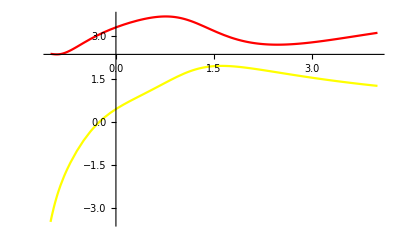

```mathematica
img1=Plot[x[t],{t,-1,4},PlotStyle->Red];
img2=Plot[y[t],{t,-1,4},PlotStyle->Yellow];
Show[img1,img2,PlotRange->All]
```

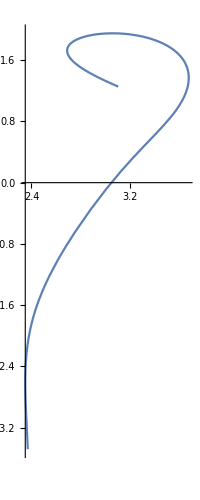

```mathematica
ParametricPlot[{x[t],y[t]},{t,-1,4},PlotRange->Automatic]
```